## 情報数学レポート 1SC16309Y田中雅也

## 課題

### 問題1

5Ω, 2Ω, 15Ω, 6Ω, 100Ωが下図のように接続されていて,それぞれの抵抗を流れる電流を I1, I2, I3, I4, I5 とする.
但し, I1, I2, I3, I4 は左から右, I5 は下から上に流れる電流値とする.回路の左から右に 2 A の直流電流が流れているとき,
I1, I2, I3, I4, I5 の値を求めよ.

#### 連立方程式Piecewise[{{I1+I2=2 I2=I4+I5 I1+I5=I3 5I1=2I2+100I5 6I4=100I5+15I3, □}}]を解く 1.Solveを用いて解く

```mathematica
Solve[{a+b==2,b==d+e,a+e==c,5a==2b+100e,6d==100e+15c},{a,b,c,d,e}]
```

{{a→4/7,b→10/7,c→4/7,d→10/7,e→0}}

#### 2.逆行列を用いて解く

```mathematica
A=({{1, 1, 0, 0, 0}, {0, 1, 0, -1, -1}, {1, 0, -1, 0, 1}, {5, -2, 0, 0, -100}, {0, 0, -15, 6, -100}})
{{1,1,0,0,0},{0,1,0,-1,-1},{1,0,-1,0,1},{5,-2,0,0,-100},{0,0,-15,6,-100}}
Inverse[A].{2,0,0,0,0}
```

{{1,1,0,0,0},{0,1,0,-1,-1},{1,0,-1,0,1},{5,-2,0,0,-100},{0,0,-15,6,-100}}

{{1,1,0,0,0},{0,1,0,-1,-1},{1,0,-1,0,1},{5,-2,0,0,-100},{0,0,-15,6,-100}}

{4/7,10/7,4/7,10/7,0}

#### まとめ

(I1,I2,I3,I4,I5)=(4/7,10/7,4/7,10/7,0)

### 問題2.

行列(□ | 9 | □
□ | □ | □
□ | □ | □)の中に,
３つの行の和,３つの列の和,２つの対角線の和が,
全て１５になるように,□の中に入る正の整数の組を全て求めよ.

#### 連立方程式を解く.

```mathematica
Solve[{s+9+t==15,u+v+w==15,x+y+z==15,s+u+x==15,v+9+y==15,t+w+z==15,s+v+z==15,t+v+x==15},{s,t,u,v,w,x,y,z}]
```

Solve::svars: 方程式はすべての"solve"変数に対しては解を与えない可能性があります．

```mathematica
{{t->6-s,u->11-2 s,v->5,w->-1+2 s,x->4+s,y->1,z->10-s}}
```

以上より、(s,t,u,v,w,x,y,z)=(1,5,9,5,1,5,1,9),(2,4,7,5,3,6,1,8),(3,3,5,5,5,7,1,7),(4,2,3,5,7,8,1,6),(5,1,1,5,9,9,1,5)を得る.

### 問題3.

次の関数の極値を求めよ.
5 x^2-4xy+8 y^2+20x/√5-80y/√5+4=0
の中心の座標と２つの楕円の軸の直線の方程式を求めよ

#### 曲線を行列を使って表現する.

```mathematica
A=.
```

```mathematica
A=({{5, -2}, {-2, 8}})
```

{{5,-2},{-2,8}}

```mathematica
Simplify[({{x, y}}).({{5, -2}, {-2, 8}}).( {{x}, {y}} )+( 20/(√5) -80/(√5) ).( {{x}, {y}} )+4]
```

{{4+5 x^2-4 x y+8 y^2+(-12 √5).{{x},{y}}}}

#### Aの固有ベクトルを求める.

```mathematica
Eigenvectors[A]
```

{{-1,2},{2,1}}

```mathematica
Eigenvalues[A]
```

{9,4}

#### Aの固有ベクトルを正規直交化する.

```mathematica
Orthogonalize[Eigenvectors[A]]
```

{{-1/(√5),2/(√5)},{2/(√5),1/(√5)}}

#### 正規直交化した固有ベクトルを列ベクトルに持つ行列Pを定義する.

```mathematica
P=Transpose[Orthogonalize[Eigenvectors[A]]];
P//MatrixForm
```

(-1/(√5) | 2/(√5)
2/(√5) | 1/(√5))

#### 行列の積P^tAPを計算してみると対角行列になる.

```mathematica
Simplify[Transpose[P].A.P]//MatrixForm
```

(9 | 0
0 | 4)

#### P(a b)を計算し、曲線の指揮を簡単にする.

```mathematica
P.({{a}, {b}})
```

```mathematica
{{-a/(√5)+(2 b)/(√5)},{(2 a)/(√5)+b/(√5)}}
```

```mathematica
f=5 x^2-4x y+8 y^2+20/(√5)x-80/(√5)y+4
```

4+4 √5 x+5 x^2-16 √5 y-4 x y+8 y^2

```mathematica
Simplify[f/.{x->-a/(√5)+(2b)/(√5),y->(2a)/(√5)+b/(√5)}]
```

-36 a+9 a^2+4 (-1+b)^2

#### 簡単な曲線の式のグラフを描く.

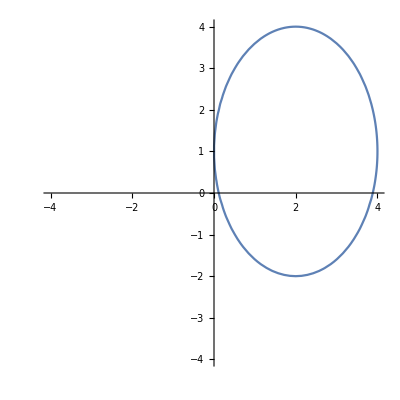

```mathematica
ContourPlot[-36a+9 a^2+4(-1+b)^2==0,{a,-4,4},{b,-4,4},Axes->True,Frame->False]
```

```mathematica
平方完成すると、9(a-2)^2+4(b-1)^2-36=0となり、ここで(c,d)=(a-2,b-1)と置換すると標準形 c^2/4+d^2/9=1を得る。
```

```mathematica
Simplify[f/.{x->-(c+2)/(√5)+(2(d+1))/(√5),y->(2(c+2))/(√5)+(d+1)/(√5)}]
```

9 c^2+4 (-9+d^2)

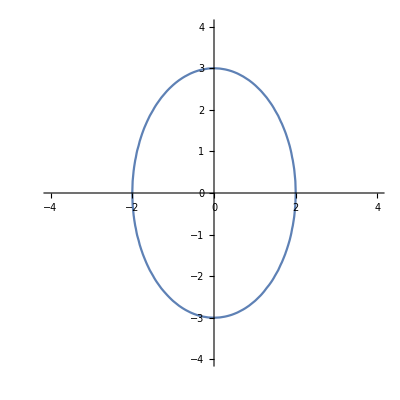

```mathematica
ContourPlot[9 c^2+4 (-9+d^2)==0,{c,-4,4},{d,-4,4},Axes->True,Frame->False]
```

#### 簡単な曲線のグラフでのd軸(c=0)のxy平面における式を求める.

```mathematica
Solve[{x==-(c+2)/(√5)+(2(d+1))/(√5),y==(2(c+2))/(√5)+(d+1)/(√5),c==0},{y},{c,d}]
```

{{y→1/2 (2 √5+x)}}

#### 簡単な曲線のグラフでのc軸(d=0)のxy平面における式を求める.

```mathematica
Solve[{x==-(c+2)/(√5)+(2(d+1))/(√5),y==(2(c+2))/(√5)+(d+1)/(√5),d==0},{y},{c,d}]
```

{{y→√5-2 x}}

#### 元の曲線のグラフ中にc軸（緑）とd軸（赤）を重ねて描く.

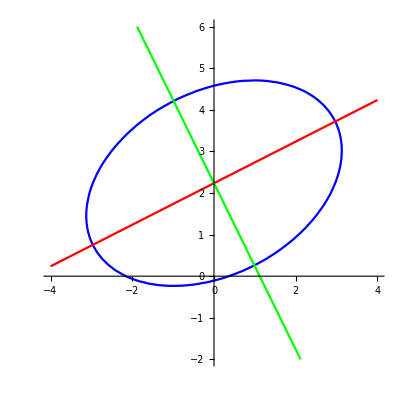

```mathematica
ContourPlot[{5 x^2-4x y+8 y^2+20/(√5)x-80/(√5)y==4,y==1/2(2 √5+x),y==√5-2x},{x,-4,4},{y,-2,6},Axes->True,Frame->False,ContourStyle->{Blue,Red,Green}]
```

#### まとめ

中心座標(0,√5)、軸の方程式y=1/2(2 √5+x),y=√5-2x